12/02/2015
Simulate coloured LE; construct histogram of positions.

```mathematica
fL[x_]:=(1-HeavisideTheta[x+X]-HeavisideTheta[x-X]);
ηproc=OrnsteinUhlenbeckProcess[0,0.5,1,0];
xQproc=StratonovichProcess[ⅆx[t]==-1*b x ⅆt+ⅆη[t],
x[t],{x,0},t,η\[Distributed]ηproc];
xLproc=StratonovichProcess[ⅆx[t]==b X fL[x]ⅆt+ⅆη[t],
x[t],{x,0},t,η\[Distributed]ηproc];
```

```mathematica
pars={b->1,X->0.5};
dt=0.05;
tmax=5*10^4 dt;
```

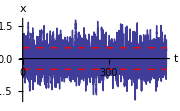

```mathematica
Show[
ListLinePlot[RandomFunction[xproc/.pars,{0.,tmax,dt}],AxesLabel->{"t","x"},Filling->Axis],
Plot[{X,-X}/.pars,{x,0,tmax},PlotStyle->{Red,Dashed}],ImageSize->Small
]
```

```mathematica
seed=39624;RandomInteger[{0,10^5}];
SeedRandom[seed]
ηdata=RandomFunction[ηproc/.pars,{0,tmax,dt}]["States"]//Flatten;
SeedRandom[seed]
xQdata=RandomFunction[xQproc/.pars,{0,tmax,dt}]["States"]//Flatten;
Qdata=Transpose[{xQdata,ηdata}];
SeedRandom[seed]
xLdata=RandomFunction[xLproc/.pars,{0,tmax,dt}]["States"]//Flatten;
Ldata=Transpose[{xLdata,ηdata}];
mm={{Min[xQdata,xLdata],Max[xQdata,xLdata]},{Min[ηdata],Max[ηdata]}};
```

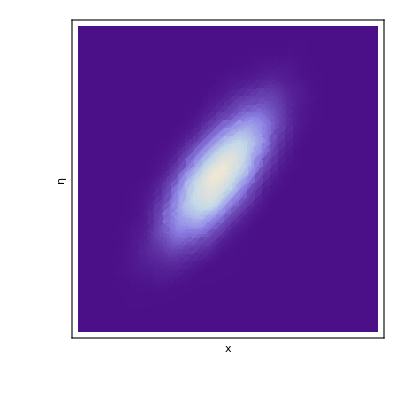

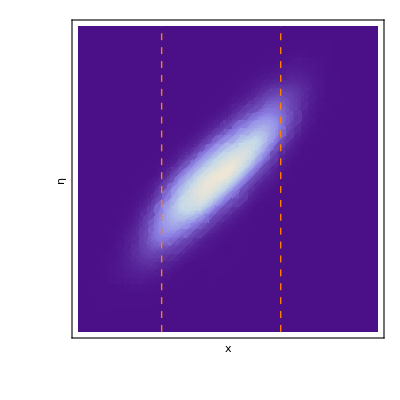

```mathematica
(* Measured positions in phase space *)
Qhist=SmoothDensityHistogram[Qdata,Automatic,"PDF",
Mesh->6,MeshStyle->Directive[Black,Thick],
FrameLabel->{Style["x",Italic,Bold,FontSize->18],Style["η",Bold,Italic,FontSize->18]},
Frame->True,FrameTicks->None,
PlotRange->mm];
Lhist=SmoothDensityHistogram[Ldata,Automatic,"PDF",
Mesh->6,MeshStyle->Directive[Black,Thick],
FrameLabel->{Style["x",Italic,Bold,FontSize->18],Style["η",Bold,Italic,FontSize->18]},
Frame->True,FrameTicks->None,
PlotRange->mm];
Qhist
Lhist=Show[Lhist,
Graphics[{Orange,Dashed,
Line[{{-0.5,mm[[2,1]]},{-0.5,mm[[2,2]]}}],Line[{{0.5,mm[[2,1]]},{0.5,mm[[2,2]]}}]}]
]
```

```mathematica
Manipulate[
SmoothDensityHistogram[Qdata[[;;i]],Automatic,"PDF",
Mesh->6,MeshStyle->Directive[Black,Thick],
FrameLabel->{Style["x",Italic,Bold,FontSize->18],Style["η",Bold,Italic,FontSize->18]},
Frame->True,FrameTicks->None],
{{i,50},50,Length[xQdata],1}]
```

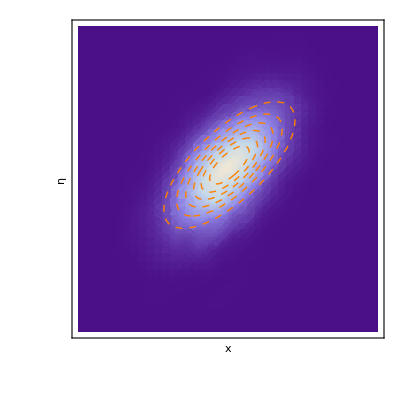

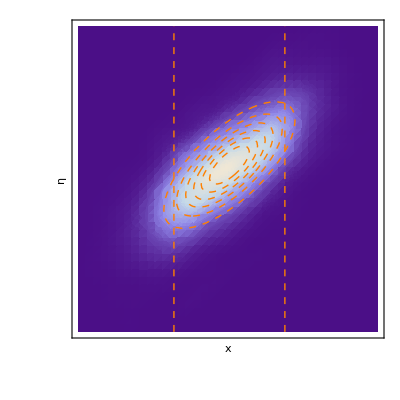

```mathematica
(* PREDICTION *)

covmat=1/(2 √2){{1/(b+1)^2,1/(2b(b+1))},{1/(2b(b+1)),1/(b+1)}}/.pars;
QhistP=Show[Qhist,
ContourPlot[PDF[MultinormalDistribution[{0,0},covmat],{x,η}],{x,-3,3},{η,-3,3},
PlotRange->All,Contours->6,ContourStyle->Directive[Orange,Thick,Dashed],ContourShading->None]
]
LhistP=Show[Lhist,
ContourPlot[PDF[MultinormalDistribution[{0,0},covmat],{x,η}],{x,-3,3},{η,-3,3},
PlotRange->All,Contours->6,ContourStyle->Directive[Orange,Thick,Dashed],ContourShading->None]
]
```

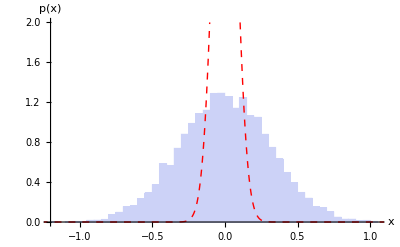

```mathematica
Show[
Histogram[xQdata,Automatic,"PDF",
AxesLabel->{"x","p(x)"}],
Plot[1/(√(2π covmat[[1,1]]))Exp[-1/2(x-0)^2/covmat[[1,1]]],{x,-3,3},
PlotStyle->{Red,Dashed},PlotRange->{Automatic,{0,2}}]
]
```